```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Psuccess[n_,Pprep_]:=1-(1-Pprep)^n;
data[Pprep_]:=Table[{n,Psuccess[n,Pprep]},{n,1,10}];
```

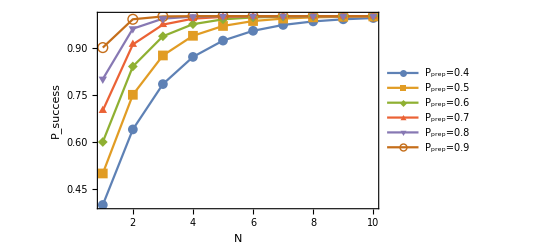

```mathematica
ListLinePlot[{data[0.4],data[0.5],data[0.6],data[0.7],data[0.8],data[0.9]},Frame->True,FrameLabel->{"N","P_success"},PlotRange->{{1,10},{0.4,1}},PlotLegends->{"P_prep=0.4","P_prep=0.5","P_prep=0.6","P_prep=0.7","P_prep=0.8","P_prep=0.9"},LabelStyle->{FontSize->15},PlotMarkers->{Automatic, 10}]
```